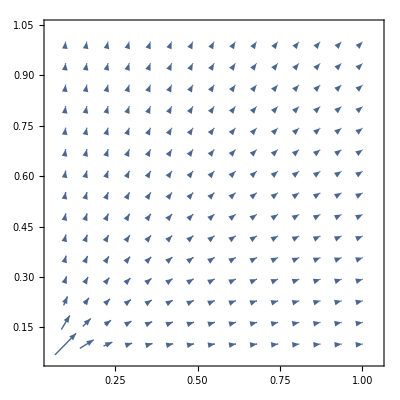

```mathematica
VectorPlot[{1/(x^2+y^2)^(3/2)*(x),1/(x^2+y^2)^(3/2)*(y)},{x,.1,1},{y,.1,1}]
```

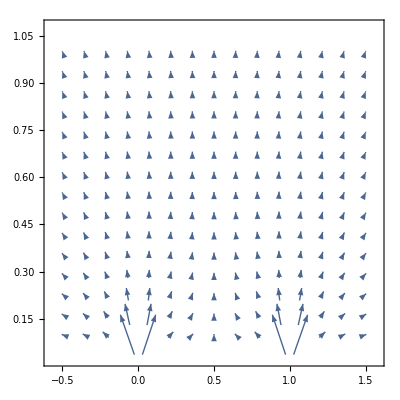

```mathematica
VectorPlot[{x/(x^2+y^2)^(3/2)+(x-1)/((x-1)^2+y^2)^(3/2),y/(x^2+y^2)^(3/2)+y/((x-1)^2+y^2)^(3/2)},{x,-.5,1.5},{y,0.10,1}]
```

```mathematica
ElectricField[x_,y_]:={x/(x^2+y^2)^(3/2)+(x-1)/((x-1)^2+y^2)^(3/2),y/(x^2+y^2)^(3/2)+y/((x-1)^2+y^2)^(3/2)}
```

```mathematica
ElectricField[0,1]
```

{-1/(2 √2),1+1/(2 √2)}

```mathematica
Dot[ElectricField[0,1],ElectricField[0,1]]
```

1/8+(1+1/(2 √2))^2

```mathematica
Sqrt[%]
```

√(1/8+(1+1/(2 √2))^2)

```mathematica
N[%]
```

1.39897